### Functions

```mathematica
Null
```

```mathematica
Null
```

## Caso K - theory

### The model

Variable definition.
In this section the effective potential is defined through descriptors.

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
Print["VH3="]
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]}
Print["V03="]
VO3=AO3 PowerExpand[(ρ^((q-6)/2)τ^-3)/.changmoduli]/.{ϕ->Log[1/s]}/.{q->3}
Print["AF5="]
VF5=AF5 PowerExpand[(ρ^(3-p)τ^-4)/.changmoduli]/.{ϕ->Log[1/s]}/.{p->5}
VF5=AF5/τ^4;
Print["VF3="]
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]}
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
Vins=AA Exp[-aa τ];
(*VD5=AD5/(√(s^3) τ^(3/2));*)
Print["Vreal = "]
Vreal=VH3+VF3+VD5+VF5+VO3+0Vins
var={s,τ};
NM=Length[var];
(*
Potential descriptors section:
 mij .......... is the hessian of the potential        |
detmij ....... is the determinant of the hessian      |
trmij ........ is the trace of the hessian            |
diV .......... is the divergent of the potential      |
egval ........ stores the eigenvalues of the hessian  |
pfun ......... the function which likely evaluates    |
               the potential and extract the egvals   |
               which later are used to return a value |
               $\lambda_1,2$ $\leq$ 0. This value is  |
                 the sum of both egvals or 0 for each   |
                 semidefinite positive egval            |
 *)
Print["Hessian of the potential = "]
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]]
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
```

VH3=

(AH3 s)/τ^3

V03=

AO3/τ^3

AF5=

AF5/τ^4

VF3=

AF3/(s τ^3)

Vreal =

AF5/τ^4+AO3/τ^3+AF3/(s τ^3)+(AH3 s)/τ^3+AD5/(√s τ^(5/2))

Hessian of the potential =

{{(8 AF3+3 AD5 √s √τ)/(4 s^3 τ^3),(-12 AH3+(12 AF3)/s^2+(5 AD5 √τ)/s^(3/2))/(4 τ^4)},{(-12 AH3+(12 AF3)/s^2+(5 AD5 √τ)/s^(3/2))/(4 τ^4),(80 AF5 s+48 AF3 τ+48 AO3 s τ+48 AH3 s^2 τ+35 AD5 √s τ^(3/2))/(4 s τ^6)}}

Optimization part, meta heuristic search of stable solutions.

```mathematica
(*In this part the NMinimize method is setup for the optimization
500 epochs and 40 decimal-precision in the computations*)
(*NMinimize search a global minimum based on the function, the variables and the constrains*)
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
(*Table inicialization for 'max' record, 0 as default value*)
max=100;
data=Table[0,{i,1,max}];
```

```mathematica
Do[
{min,steps}=Reap[ NMinimize[
{
(*The function to minimize*)
10^4 diV.diV+ 10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij),
(*The given constrains about the s and $\tau$ domain 0 < s, $\tau$ $\leq$ 1*)
s>RandomInteger[{1,100}]/100,
τ>RandomInteger[{1,100}]/100
},
(*Variables to minimize over*)
{s,τ,AF3,AH3,AO3,AF5,AD5},
Method->{
"SimulatedAnnealing", (*Metaheuristic optimization with Simulated annealing*)
"PerturbationScale"->0.5,
"LevelIterations"->50,
"RandomSeed"->0,
"PostProcess"->{ (*Numeric method to find a less stochastic (more precise) minimum point, in other words, refine the search*)
FindMinimum,(*Here, this searches local minimum, since the SA found a possible good candidate, this refines*)
Method->"ConjugateGradient",
MaxIterations-> 500,
PrecisionGoal->10^2,(*High decimal-precision handle, /M/e-100*)
WorkingPrecision->500 (*Heavy decimal-precision handle, /M/e-500*)
}
},
(*Log, print a structure of data in the form '{var_symbol -> /value/, ...}'*)
StepMonitor:>Sow[{s,τ,AF3,AH3,AO3,AA,aa}]
] (*End NMinimize*)
];(*End Reap *)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[ Mod[taur,10]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}
](*End Do*)
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,3},{τ,0,5.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
vars={s,τ,AF3,AH3,AO3,AA,aa};(*|0|*)
ListLogPlot[Table[(10^4 diV.diV+10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij))/.Thread[vars->steps⟦1⟧⟦jj⟧],{jj,1,100}]]
```

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
(*data=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
$MaxExtraPrecision=10000;
max=Length[data];
datag=Table[0,{i,max}];
up=Length[data⟦1⟧]-2;
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;up⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[Re[diV/.data⟦jj⟧⟦4;;up⟧/.fr]]==0.0,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;up⟧,fr,data⟦jj⟧⟦4;;up⟧,egval/.fr/.data⟦jj⟧⟦4;;up⟧}],30];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;8⟧,egval}/.data⟦jj⟧⟦4;;8⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;8⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦up+1;;up+2⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦up+1;;up+2⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1]
{ListPlot[Table[{τ/.datag⟦i⟧⟦3⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re τ","Λ"},PlotStyle-> Blue],ListPlot[Table[{s/.datag⟦i⟧⟦2⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re s","Λ"},PlotStyle-> Blue]}
(*Save["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5",datag];*)
```

```mathematica
datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5"];*)
```

```mathematica
Print["Stable dS"];
up=Length[datag⟦1⟧]-2;
aux1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Print["dS ",Length[aux1],". Anda the % dS is ",N@Length[aux1]/Length[datag] 100];
aux11=Table[If[ii==1,{"i","min V","m^2","m^2","s","τ","AF3","AH3","AF5","AO3","AD5"},
Flatten[{ii,aux1⟦ii⟧⟦2;;4⟧,Flatten[{s,τ,AF3,AH3,AF5,AO3,AD5,AA}/.aux1⟦ii⟧⟦5;;⟧]}]],{ii,Length[aux1]}];
Grid[N[aux11,4], Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
Print["Stable AdS"];
aux2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
aux22=Table[If[ii==1,{"min V","m^2","m^2","s","τ","AF3","AH3","AF5","AO3","AD5"},
Flatten[{aux2⟦ii⟧⟦2;;4⟧,Flatten[{s,τ,AF3,AH3,AF5,AO3,AD5,aa,AA}/.aux2⟦ii⟧⟦5;;⟧]}]],{ii,Length[aux2]}];
Print["dS ",Length[aux2],". And the % of AdS is ",N@Length[aux2]/Length[datag] 100];
Grid[aux22, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

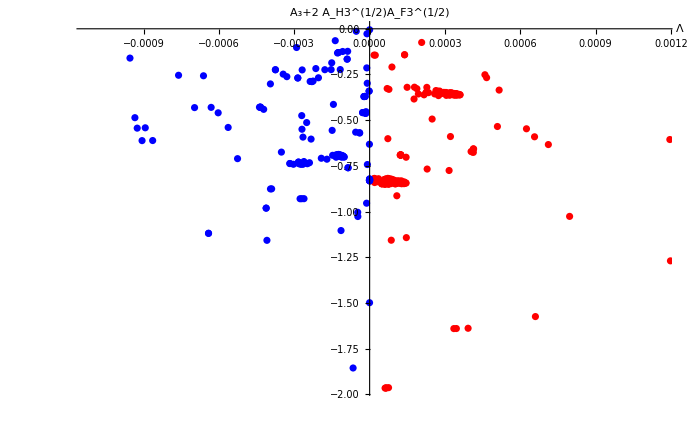

{{-0.00012464,-0.13},{-0.00039013,-0.8755},{-0.00014738,-0.6921},{-0.001391,-0.5234},{-0.00043569,-0.4291},{-0.00028337,-0.7291},{-0.000066456,-0.63967+0.10601 ⅈ},{-0.00015331,-0.2233},{-0.00042185,-0.4406},{-0.00012303,-0.6922},{-0.0002654,-0.5925},{-1.082×10^-7,-0.8223},{-0.00015092,-0.186},{-0.000018687,-0.3704},{-0.000023066,-0.3707},{-0.000040394,-0.5681},{-0.0002787,-0.42878+0.10967 ⅈ},{-0.00024805,-0.738},{-0.00012464,-0.13},{-0.00012293,-0.6884},{-0.00027035,-0.9294},{-0.00032964,-0.2619},{-0.0001369,-0.06503},{-0.000065209,-0.59035+0.11487 ⅈ},{-0.00013192,-0.6884},{-0.00026865,-0.225},{-0.000020494,-0.3704},{-0.000086673,-0.7601},{-0.00152,-0.3707},{-0.00010326,-0.7012},{-7.7393×10^-7,-0.829},{-0.00023316,-0.6033},{-0.000046925,-1.027},{-0.00011634,-0.6896},{-0.00012388,-0.6871},{-2.92×10^-8,-0.8287},{-0.00023685,-0.2881},{-0.00014418,-0.4136},{-0.0002613,-0.9292},{-0.000089468,-0.166},{-0.0001155,-0.6948},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00069702,-0.4311},{-0.00001461,-0.4534},{-0.00010828,-0.6935},{-0.00012027,-0.6959},{-0.00026936,-0.5495},{-0.00027696,-0.9296},{-0.00086381,-0.6113},{-0.001516,-0.3704},{-8.9965×10^-6,-0.7425},{-0.0009542,-0.1603},{-3.832×10^-7,-0.8288},{-0.00056327,-0.5397},{-0.00045495,-1.0037+0.14476 ⅈ},{-0.0002617,-0.7261},{-0.001487,-0.3686},{-0.000027974,-0.4585},{-0.00026535,-0.7399},{-0.00027105,-0.42869+0.10959 ⅈ},{-0.00011391,-1.104},{-0.00031757,-0.737},{-0.00020248,-1.6904+0.18222 ⅈ},{-0.00029086,-0.102},{-0.00020382,-0.2679},{-0.000089468,-0.166},{-0.00017839,-0.2238},{-0.002193,-0.8576},{-0.00022977,-0.2886},{-0.00012491,-0.6897},{-0.000053287,-0.0137},{-0.000012134,-0.9541},{-0.00019241,-0.7082},{-0.000015058,-0.4624},{-0.00012027,-0.6959},{-0.00039511,-0.3015},{-0.00013353,-0.7025},{-0.000027974,-0.4585},{-0.000016875,-0.4627},{-0.00034423,-0.248},{-0.00152,-0.3707},{-2.0643×10^-9,-0.0055},{-0.00027389,-0.7416},{-0.00008747,-0.123},{-2.264×10^-7,-0.8257},{-0.00011702,-0.223},{-0.00026535,-0.7399},{-1.1552×10^-6,-0.8281},{-0.00090608,-0.6117},{-8.1068×10^-7,-0.65609+0.16922 ⅈ},{-0.0013072,-0.3945},{-0.00022977,-0.2886},{-0.00012793,-0.1325},{-0.00063101,-0.4299},{-0.00022513,-0.286},{-0.00010573,-0.6974},{-0.00093453,-0.4862},{-0.00043411,-0.4284},{-0.000060548,-1.4939+0.42352 ⅈ},{-0.00013409,-0.6971},{-2.0834×10^-6,-0.3409},{-0.00064147,-1.119},{-2.264×10^-7,-0.8257},{-0.000047477,-1.004},{-0.000065847,-1.855},{-0.00025066,-0.513},{-5.0599×10^-6,-0.69327+0.22791 ⅈ},{-0.00037512,-0.2241},{-0.0003948,-0.8759},{-0.000085233,-0.7603},{-0.00011387,-0.7008},{-0.00041198,-0.9809},{-0.00089334,-0.5416},{-0.000017245,-0.37},{-0.0004089,-1.157},{-0.00012027,-0.6959},{-0.00076075,-0.2543},{-0.00035129,-0.6746},{-3.4703×10^-7,-0.65842+0.20357 ⅈ},{-0.00060304,-0.4596},{-0.001457,-0.3668},{-0.00028601,-0.2691},{-0.00092536,-0.5435},{-0.000022105,-0.3707},{-0.000019107,-0.37},{-0.0005259,-0.7103},{-0.00030339,-0.7411},{-0.00043569,-0.4291},{-0.0001074,-0.1242},{-0.00014924,-0.5557},{-0.00010911,-0.57674+0.14944 ⅈ},{-1.6644×10^-6,-0.65565+0.16683 ⅈ},{-6.79×10^-9,-0.8208},{-0.00010573,-0.6974},{-0.000034012,-0.5654+0.15708 ⅈ},{-0.00028337,-0.7291},{-2.0432×10^-6,-0.3408},{-3.254×10^-7,-1.498},{-0.000084681,-1.1683+0.36211 ⅈ},{-0.00021418,-0.2176},{-0.00041198,-0.9809},{-0.00043861,-0.429},{-8.247×10^-7,-0.6315},{-0.00017011,-0.7134},{-0.00011112,-0.7009},{-4.×10^-10,-0.8317},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00064147,-1.119},{-0.000011399,-0.214},{-0.00023955,-0.7326},{-0.00028207,-0.738},{-0.000039472,-0.5703},{-0.0039455,-0.4976},{-0.000010682,-0.0276},{-0.00012935,-0.6954},{-0.000018787,-0.4596},{-0.00066149,-0.257},{-0.00028731,-0.42886+0.10966 ⅈ},{-0.00028261,-0.42883+0.10971 ⅈ},{-0.00037512,-0.2241},{-9.5848×10^-6,-0.2981},{-0.00031757,-0.737},{-0.00010573,-0.6974},{-0.00027033,-0.4749},{-0.000055618,-0.5655},{-0.00028601,-0.2691},{-0.0015105,-0.3701},{-4.×10^-10,-0.8317},{-0.00010929,-0.6998},{-0.00010075,-0.7012}}

-Graphics-

{{-0.00012464,-0.13},{-0.00039013,-0.8755},{-0.00014738,-0.6921},{-0.001391,-0.5234},{-0.00043569,-0.4291},{-0.00028337,-0.7291},{-0.000066456,-0.63967+0.10601 ⅈ},{-0.00015331,-0.2233},{-0.00042185,-0.4406},{-0.00012303,-0.6922},{-0.0002654,-0.5925},{-1.082×10^-7,-0.8223},{-0.00015092,-0.186},{-0.000018687,-0.3704},{-0.000023066,-0.3707},{-0.000040394,-0.5681},{-0.0002787,-0.42878+0.10967 ⅈ},{-0.00024805,-0.738},{-0.00012464,-0.13},{-0.00012293,-0.6884},{-0.00027035,-0.9294},{-0.00032964,-0.2619},{-0.0001369,-0.06503},{-0.000065209,-0.59035+0.11487 ⅈ},{-0.00013192,-0.6884},{-0.00026865,-0.225},{-0.000020494,-0.3704},{-0.000086673,-0.7601},{-0.00152,-0.3707},{-0.00010326,-0.7012},{-7.7393×10^-7,-0.829},{-0.00023316,-0.6033},{-0.000046925,-1.027},{-0.00011634,-0.6896},{-0.00012388,-0.6871},{-2.92×10^-8,-0.8287},{-0.00023685,-0.2881},{-0.00014418,-0.4136},{-0.0002613,-0.9292},{-0.000089468,-0.166},{-0.0001155,-0.6948},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00069702,-0.4311},{-0.00001461,-0.4534},{-0.00010828,-0.6935},{-0.00012027,-0.6959},{-0.00026936,-0.5495},{-0.00027696,-0.9296},{-0.00086381,-0.6113},{-0.001516,-0.3704},{-8.9965×10^-6,-0.7425},{-0.0009542,-0.1603},{-3.832×10^-7,-0.8288},{-0.00056327,-0.5397},{-0.00045495,-1.0037+0.14476 ⅈ},{-0.0002617,-0.7261},{-0.001487,-0.3686},{-0.000027974,-0.4585},{-0.00026535,-0.7399},{-0.00027105,-0.42869+0.10959 ⅈ},{-0.00011391,-1.104},{-0.00031757,-0.737},{-0.00020248,-1.6904+0.18222 ⅈ},{-0.00029086,-0.102},{-0.00020382,-0.2679},{-0.000089468,-0.166},{-0.00017839,-0.2238},{-0.002193,-0.8576},{-0.00022977,-0.2886},{-0.00012491,-0.6897},{-0.000053287,-0.0137},{-0.000012134,-0.9541},{-0.00019241,-0.7082},{-0.000015058,-0.4624},{-0.00012027,-0.6959},{-0.00039511,-0.3015},{-0.00013353,-0.7025},{-0.000027974,-0.4585},{-0.000016875,-0.4627},{-0.00034423,-0.248},{-0.00152,-0.3707},{-2.0643×10^-9,-0.0055},{-0.00027389,-0.7416},{-0.00008747,-0.123},{-2.264×10^-7,-0.8257},{-0.00011702,-0.223},{-0.00026535,-0.7399},{-1.1552×10^-6,-0.8281},{-0.00090608,-0.6117},{-8.1068×10^-7,-0.65609+0.16922 ⅈ},{-0.0013072,-0.3945},{-0.00022977,-0.2886},{-0.00012793,-0.1325},{-0.00063101,-0.4299},{-0.00022513,-0.286},{-0.00010573,-0.6974},{-0.00093453,-0.4862},{-0.00043411,-0.4284},{-0.000060548,-1.4939+0.42352 ⅈ},{-0.00013409,-0.6971},{-2.0834×10^-6,-0.3409},{-0.00064147,-1.119},{-2.264×10^-7,-0.8257},{-0.000047477,-1.004},{-0.000065847,-1.855},{-0.00025066,-0.513},{-5.0599×10^-6,-0.69327+0.22791 ⅈ},{-0.00037512,-0.2241},{-0.0003948,-0.8759},{-0.000085233,-0.7603},{-0.00011387,-0.7008},{-0.00041198,-0.9809},{-0.00089334,-0.5416},{-0.000017245,-0.37},{-0.0004089,-1.157},{-0.00012027,-0.6959},{-0.00076075,-0.2543},{-0.00035129,-0.6746},{-3.4703×10^-7,-0.65842+0.20357 ⅈ},{-0.00060304,-0.4596},{-0.001457,-0.3668},{-0.00028601,-0.2691},{-0.00092536,-0.5435},{-0.000022105,-0.3707},{-0.000019107,-0.37},{-0.0005259,-0.7103},{-0.00030339,-0.7411},{-0.00043569,-0.4291},{-0.0001074,-0.1242},{-0.00014924,-0.5557},{-0.00010911,-0.57674+0.14944 ⅈ},{-1.6644×10^-6,-0.65565+0.16683 ⅈ},{-6.79×10^-9,-0.8208},{-0.00010573,-0.6974},{-0.000034012,-0.5654+0.15708 ⅈ},{-0.00028337,-0.7291},{-2.0432×10^-6,-0.3408},{-3.254×10^-7,-1.498},{-0.000084681,-1.1683+0.36211 ⅈ},{-0.00021418,-0.2176},{-0.00041198,-0.9809},{-0.00043861,-0.429},{-8.247×10^-7,-0.6315},{-0.00017011,-0.7134},{-0.00011112,-0.7009},{-4.×10^-10,-0.8317},{-0.0004495,-1.0036+0.14576 ⅈ},{-0.00064147,-1.119},{-0.000011399,-0.214},{-0.00023955,-0.7326},{-0.00028207,-0.738},{-0.000039472,-0.5703},{-0.0039455,-0.4976},{-0.000010682,-0.0276},{-0.00012935,-0.6954},{-0.000018787,-0.4596},{-0.00066149,-0.257},{-0.00028731,-0.42886+0.10966 ⅈ},{-0.00028261,-0.42883+0.10971 ⅈ},{-0.00037512,-0.2241},{-9.5848×10^-6,-0.2981},{-0.00031757,-0.737},{-0.00010573,-0.6974},{-0.00027033,-0.4749},{-0.000055618,-0.5655},{-0.00028601,-0.2691},{-0.0015105,-0.3701},{-4.×10^-10,-0.8317},{-0.00010929,-0.6998},{-0.00010075,-0.7012}}

-Graphics-

```mathematica
up=Length[datag⟦1⟧]-2;
datag1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
datag2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{datag1⟦jj⟧⟦1⟧,(AO3+2 AH3^(1/2)AF3^(1/2))/.datag1⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag1]}];
l2=Table[{datag2⟦jj⟧⟦1⟧,(AO3+2 AH3^(1/2)AF3^(1/2))/.datag2⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag2]}];
l2
f1=ListPlot[{l1,l2},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20},AxesLabel->{"Λ","A_3+2 A_H3^(1/2)A_F3^(1/2)"},ImageSize->700]
```

```mathematica
inter=aux1⟦6⟧⟦1⟧;
Print["values = ",datag⟦inter⟧];
Vold=Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧;
eqs=Table[D[Vold,var⟦i⟧],{i,1,2}];
sol=Quiet@Solve[Thread[%==0],var]⟦2⟧;
Print["AdS: Exact solution: ",{(AF3/AH3)^(1/2),(-4/3)AF5/(AO3+2 AH3^(1/2)AF3^(1/2))}/.datag⟦inter⟧⟦4;;up⟧,"vs numerical sol: ",sol];
(*******************************************)
poly=(Expand[-2 AF3^3+3 AF3^2 AO3 s+(AD5^2 AF5+12 AF3^2 AH3) s^2-6 AF3 AH3 AO3 s^3-18 AF3 AH3^2 s^4+3 AH3^2 AO3 s^5+8 AH3^3 s^6]);
auxsols=N[NSolve[(poly/.Rationalize[datag⟦inter⟧⟦4;;8⟧,10^-100])==0,s,WorkingPrecision->10]⟦5⟧,30];
Print["dS: Exact solution: ",{s/.auxsols,(4(-AF3+AH3 s^2)^2)/(AD5^2 s)/.Rationalize[datag⟦inter⟧⟦4;;8⟧,10^-100]/.auxsols}," vs numerical sol: ",datag⟦inter⟧⟦2;;3⟧];
(*******************************************)
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧," -> ",diV/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol]
Print[sol,"->",datag⟦inter⟧⟦2;;3⟧];
Print[Eigenvalues[mij/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol],"->",datag⟦inter⟧⟦up+1;;up+2⟧];
Print["V = ",Vold/.sol,"-> V = ",datag⟦inter⟧⟦1⟧];
{fo=Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"},PlotStyle->Blue,ImageSize->{300}],
foτ=Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]2.1},PlotStyle->Blue,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{300}]}
{fn=Plot[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,{s,Evaluate[(s/.sol⟦1⟧)] 0.9,Evaluate[(s/.sol⟦1⟧)]1.1},PlotStyle->Red,ImageSize->{300},BaseStyle->{FontSize->20,FontFamily->"Times"}],
Plot[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,{τ,Evaluate[(τ/.sol⟦2⟧)] 0.9,Evaluate[(τ/.sol⟦2⟧)]1.1},PlotStyle->Red,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{300}]}
```

```mathematica
Plot[{Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,Vreal/.datag⟦inter⟧⟦3;;up⟧},{s,Evaluate[(s/.sol⟦1⟧)] 0.5,Evaluate[(s/.sol⟦1⟧)]2.5},PlotRange->{-0.062,0.005},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{700}]
Plot[{Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧},{τ,Evaluate[(τ/.sol⟦2⟧)] 0.5,Evaluate[(τ/.sol⟦2⟧)]5.5},PlotRange->{-0.062,0.0062},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},Epilog->Inset[foτ,{6,-0.04}],ImageSize->{700}]
```

```mathematica
(*Plot[{Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧},{τ,Evaluate[(τ/.sol⟦2⟧)] 0.95,Evaluate[(τ/.sol⟦2⟧)]25.5},AxesLabel->{"τ","V"},PlotRange->{-0.001,0.0062},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{700}]*)
Veff=Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧;
ϕfv1=τ/.datag⟦inter⟧⟦2;;3⟧⟦2⟧
edo[ϕfv_,Vreal1_]:={s D[τp[s],s,s]+3 D[τp[s],s]==s(D[Vreal1,τ]/.τ->τp[s]),τp[10^2]==ϕfv,τp'[1/1000]==0.0};
NDSolve[edo[ϕfv1,Veff],τp[s],{s,1,1000}]
```

```mathematica
inter=1616;
Print["values = ",datag⟦inter⟧];
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧]
Vold=Rationalize[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧,10^-1000];
eqs=Table[D[Vold,var⟦i⟧],{i,1,2}];
sol=N@Solve[Thread[%==0],var]⟦2⟧
Print[Eigenvalues[mij/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol],"->",datag⟦inter⟧⟦up+1;;up+2⟧];
Print["V = ",datag⟦inter⟧⟦1⟧,"-> V = ",Vold/.sol];
{Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"}],
Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"τ","V"}]}
Plot3D[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1}]
```

```mathematica
(*Save["C:\\Users\\Cesar\\Dropbox\\Source-codes\\penalty-cases-AdS-noT",data]*)
```

```mathematica
caseso3gp⟦1⟧
```

```mathematica
caseso3=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g"];
f1=ListPlot[Table[{Min[caseso3⟦i⟧⟦9;;10⟧],caseso3⟦i⟧⟦1⟧},{i,Length[caseso3]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o7g"];
f2=ListPlot[Table[{Min[caseso3g⟦i⟧⟦9;;10⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g"];
f3=ListPlot[Table[{Min[caseso3g⟦i⟧⟦8;;9⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Green,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g-pos"];
f4=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦8;;9⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
f5=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦10;;11⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3F5=Get["/Users/cesar/Dropbox/Source-codes/penalty-F5-o3g-noD5-2"];
f6=ListPlot[Table[{Min[caseso3F5⟦i⟧⟦8;;9⟧],caseso3F5⟦i⟧⟦1⟧},{i,Length[caseso3F5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
casenoARnp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty"];
f8=ListPlot[Table[{Min[casenoARnp⟦i⟧⟦9;;10⟧],casenoARnp⟦i⟧⟦1⟧},{i,Length[casenoARnp]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
(*caseoscar=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-oscarproposal"];
f9=ListPlot[Table[{Min[caseoscar⟦i⟧⟦9;;10⟧],caseoscar⟦i⟧⟦1⟧},{i,Length[caseoscar]}],BaseStyle->{FontSize->20},PlotMarkers->{"\[KernelIcon]",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];*)

(*Show[f5,f6,f1,f3,f2]*)
Show[f7,f10]
casenoARnod5⟦1⟧
casenoAR⟦1⟧
(*penalty-random-o3g-noAR6*)
```

```mathematica
casenoARnod5=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-noD5"];
f10z=ListPlot[Table[{Min[casenoARnod5⟦i⟧⟦8;;9⟧],casenoARnod5⟦i⟧⟦1⟧},{i,Length[casenoARnod5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","|Λ|"},PlotStyle-> Black,ImageSize->700,PlotRange->{{0.0,0.002},{0.0,-0.002}}];
f10=ListPlot[Table[{Min[casenoARnod5⟦i⟧⟦8;;9⟧],casenoARnod5⟦i⟧⟦1⟧},{i,Length[casenoARnod5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7z=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700,PlotRange->{{0.0,0.002},{-0.002,0.002}}];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
Show[f7z,f10z]
(*Show[f5,f6,f1,f3,f2]*)
```

### Machine learning

```mathematica
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
up=Length[datag⟦1⟧]-2;
varsNN={AF3,AH3,AD5,AO3,AF5};
dataNNv=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->Chop[datag⟦jj⟧⟦1⟧],{jj,1,Length[datag]}]
frac=0.3;
{nvs2tes,nvs2tra}=TakeDrop[dataNNv,Round[frac*Length[dataNNv]]];
net=NetChain[{32,Tanh,1},"Input"-> {5},"Output"->"Scalar"];
(*net=NetInitialize[net]*)
trainedv=NetTrain[net,nvs2tra,ValidationSet->nvs2tes,TargetDevice->"CPU"]
(*net=NetChain[{45,Tanh,1},"Input"->6,"Output"->"Scalar"];
traineds=NetTrain[net,dataNNs,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedτ=NetTrain[net,dataNNτ,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->1]
net1=NetTrain[net,dataNN,BatchSize->1024]*)
```

```mathematica
2
```

```mathematica
trainedv
```

```mathematica
data=Flatten@Table[{x,y}->Exp[-Norm[{x,y}]],{x,-3,3,.005},{y,-3,3,.005}];
net=NetChain[{32,Tanh,2}];
trained=NetTrain[net,data,BatchSize->1024]
```

```mathematica
NetMeasurements[trained,nvs2cv,"Accuracy"]
```

```mathematica
datag1=DeleteCases[Table[If[Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{AO3/.datag1⟦jj⟧⟦2;;up⟧,datag1⟦jj⟧⟦1⟧},{jj,1,Length[datag1]}];
ListPlot[FindClusters[l1,3,Method->"KMeans"]]
```

## Calibration

```mathematica
var={x,y};
NM=Length[var];

mij=Simplify[Table[D[f[x,y],var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
diV=Simplify[Table[D[f[x,y],var⟦i⟧],{i,1,NM}]];
Solve[Table[D[f[x,y],var⟦i⟧]==0,{i,1,2}],var]
Plot3D[f[x,y],{x,-6,6},{y,-6,6}]
pfun=α1 If[#1<0,#1^2,0]+α2 If[#2<0,#2^2,0] &;
NMinimize[f[x,y],{x,y},Method->{"SimulatedAnnealing","PenaltyFunction"->pfun}]
```

```mathematica
Plot[Exp[-(deltaF Log[1+1])/10],{deltaF,0,100}]
```

```mathematica
f[x_,y_]:=(x+2y-7)^2+(2x+y-5)^2;
f[x_,y_]:=-20 Exp[-0.2 √(0.5(x^2+y^2))]-Exp[0.5 (Cos[2π x]+Cos[2 π y])]+Exp[1]+20;
{min,steps}=Reap[
NMinimize[
{f[x,y],x>1,y>1},{x,y},
Method->{"SimulatedAnnealing","PerturbationScale"->.1,"PenaltyFunction"->Function[{x,y},Exp[x+y]]},
StepMonitor:>Sow[{x,y}]]];
Show[ContourPlot[f[x,y],{x,-2.5,2.5},{y,-3.5,3.5},Epilog->{PointSize[0.02],Point[{x,y}/.min⟦2⟧]}],ListPlot[steps,PlotStyle->Red]]
min⟦2⟧
```

## Intento 2

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
Vreal=VH3+VF3+VR6+VD5;
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},If[egval⟦1⟧<0,1000,0]+If[egval⟦2⟧<0,1000,0]+100/(s+1)+100/(τ+1)+ If[Vreal<0,1000,0]];
SetOptions[NMinimize,AccuracyGoal-> 0.001,MaxIterations->500,WorkingPrecision->40];
max=5;
data=Table[0,{i,1,max}];
Do[
invalue=Table[{RandomReal[{20,200}],RandomReal[{20,200}],RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}],RandomReal[{-10,10}]},{ii,1,50}];
{min,steps}=Reap[
NMinimize[{(diV⟦1⟧^2+diV⟦2⟧^2)+10(Abs[egval⟦1⟧]-egval⟦1⟧)+10 (Abs[egval⟦1⟧]-egval⟦1⟧)+100/(s+1)+100/(τ+1)+ 10(Abs[Vreal]-Vreal),s>5,τ>taur},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->2.5,"LevelIterations"->200,"SearchPoints"->Automatic,"InitialPoints"->invalue,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^-3,WorkingPrecision->10^3}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,400]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,10},{τ,0,150.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
Do[
ndiV=diV/.data⟦kk⟧⟦4;;7⟧;
Print["data = ",data⟦kk⟧];
Print["sol = ",NSolve[Table[ndiV⟦ii⟧==0,{ii,1,2}],{s,τ}]],{kk,1,5}]
```

```mathematica
RandomReal[{20,200},{50,6}]
```

## Caso Blumenhagen

```mathematica
Vreal=AH3/(s^2 τ^3)+(AF0 τ^3)/s^4+(AF2 τ)/s^4+AF4/(s^4 τ^1)+AD6/s^3+AD5/(s^3 τ^(1/2))+(AD7 τ^(1/2))/s^3;
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=20;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^3 diV⟦1⟧^2+10^3 diV⟦2⟧^2+10^5(Abs[Vreal]-Vreal)+10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij),s>10taur,τ>10 taur},{s,τ,AF0,AF2,AF4,AH3,AD5,AD6,AD7},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^3,WorkingPrecision->10^3,AccuracyGoal->20}},
StepMonitor:>Sow[{s,τ,AF0,AF2,AF4,AH3,AD5,AD6,AD7}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,1]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,10},{τ,0,150.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
$MaxExtraPrecision=10000;
datag=Table[0,{i,max}];
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;10⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[diV/.data⟦jj⟧⟦4;;10⟧/.fr]==0.,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;10⟧,fr,data⟦jj⟧⟦4;;10⟧,egval/.fr/.data⟦jj⟧⟦4;;10⟧}],20];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;10⟧,egval}/.data⟦jj⟧⟦4;;10⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;10⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
```

```mathematica
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦11;;12⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦11;;12⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1,f0]
```

```mathematica
datag//TableForm
```

```mathematica
VF=h^2/(8 s^2 t^3)+(f0^2 t^3)/(32 s^4)+(3 f4^2)/(32 s^4 t)- (f0 h)/(4 s^3)+(AD7 t^(1/2))/s^3;
sol=PowerExpand@Simplify@Solve[{VF==0,D[VF,s]==0,D[VF,t]==0},{s,t,AD7}];
TableForm[sol]
var={s,t};
Table[D[VF,var⟦i⟧,var⟦i⟧],{i,2},{j,2}]/.sol⟦12⟧
Eigenvalues[%]
```

```mathematica
detmij-trmij^2/4
```

```mathematica
Sin[π/6]
```

## Caso Non-geometric

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VO3=AO3 PowerExpand[(ρ^((3-6)/2)τ^-3)/.changmoduli]/.{ϕ->Log[1/s]};
VF5=AF5 PowerExpand[(ρ^(3-p)τ^-4)/.changmoduli]/.{ϕ->Log[1/s]}/.{p->5};
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
VNG=ANG/(s τ);
Vreal=VH3+VF3+VF5+VO3+VNG
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=1000;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^4 diV.diV+10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij)+0 10^3(Abs[AD5]-AD5),s>RandomInteger[{1,100}]/100,τ>RandomInteger[{1,100}]/100},{s,τ,AF3,AH3,AO3,ANG,AF5},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^2,WorkingPrecision->10^3}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AO3,ANG,AF5}]]];
(*{min,steps}=Reap[
NMinimize[
{Vreal,s>1.1,τ>2.1,diV⟦1⟧,diV⟦2⟧},{s,τ,AF3,AH3,AD5,AR6},
Method->{"SimulatedAnnealing","PerturbationScale"->1.5,"LevelIterations"->100,"RandomSeed"->10,"PenaltyFunction"->pfun,"PostProcess"->Automatic},
StepMonitor:>Sow[{s,τ,AF3,AH3,AD5,AR6}]]];*)
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,100]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,2},{τ,0,10},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

```mathematica
vars={s,τ,AF3,AH3,AO3,ANG,AF5};(*|1|*)
ListLogPlot[Table[(10^4 diV.diV+ 10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+ 10^5(Abs[trmij]-trmij)+0 10^3(Abs[AD5]-AD5))/.Thread[vars->steps⟦1⟧⟦jj⟧],{jj,1,100}]]
```

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
(*data=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];*)
$MaxExtraPrecision=10000;
max=Length[data];
datag=Table[0,{i,max}]; 
up=Length[data⟦1⟧]-2;
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;up⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[Re[diV/.data⟦jj⟧⟦4;;up⟧/.fr]]==0.0,
(*Print["--------------------------------------------------------------------------------------------"];*)
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;up⟧,fr,data⟦jj⟧⟦4;;up⟧,egval/.fr/.data⟦jj⟧⟦4;;up⟧}],30];
(*Print["values = ",{Vreal/.fr /.data⟦jj⟧⟦4;;8⟧,egval}/.data⟦jj⟧⟦4;;8⟧/.fr];
Print["diV = ",Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.data⟦jj⟧⟦4;;8⟧/.fr];*)
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦up+1;;up+2⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦up+1;;up+2⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1]
{ListPlot[Table[{τ/.datag⟦i⟧⟦3⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re τ","Λ"},PlotStyle-> Blue],ListPlot[Table[{s/.datag⟦i⟧⟦2⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re s","Λ"},PlotStyle-> Blue]}
(*Save["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty",datag];*)
```

```mathematica
(*datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];*)
```

```mathematica
Print["Stable dS"];
up=Length[datag⟦1⟧]-2;
aux1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Length[aux1]
Grid[aux1, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
Print["Stable AdS"];
aux2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Length[aux2]
Grid[aux2, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

```mathematica
Histogram[Flatten@Table[data⟦jj⟧⟦9;;10⟧,{jj,Length[data]}]]
```

```mathematica
up=Length[datag⟦1⟧]-2;
datag1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
datag2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{datag1⟦jj⟧⟦1⟧,AO3/.datag1⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag1]}];
l2=Table[{datag2⟦jj⟧⟦1⟧,AO3/.datag2⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag2]}];
f1=ListPlot[{l1,l2},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20},AxesLabel->{"Λ","A_O3"},ImageSize->700]
```

```mathematica
inter=101;
Print["values = ",datag⟦inter⟧];
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧]
{Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"}],
Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"τ","V"}]}
Plot3D[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]1.1}]
```

```mathematica
(*Save["C:\\Users\\Cesar\\Dropbox\\Source-codes\\penalty-cases-AdS-noT",data]*)
```

```mathematica
caseso3=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g"];
f1=ListPlot[Table[{Min[caseso3⟦i⟧⟦9;;10⟧],caseso3⟦i⟧⟦1⟧},{i,Length[caseso3]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o7g"];
f2=ListPlot[Table[{Min[caseso3g⟦i⟧⟦9;;10⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
caseso3g=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g"];
f3=ListPlot[Table[{Min[caseso3g⟦i⟧⟦8;;9⟧],caseso3g⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Green,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o5g-pos"];
f4=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦8;;9⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3gp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
f5=ListPlot[Table[{Min[caseso3gp⟦i⟧⟦10;;11⟧],caseso3gp⟦i⟧⟦1⟧},{i,Length[caseso3g]}],BaseStyle->{FontSize->20},PlotMarkers->{"⊙",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Cyan,ImageSize->700];
caseso3F5=Get["/Users/cesar/Dropbox/Source-codes/penalty-F5-o3g-noD5-2"];
f6=ListPlot[Table[{Min[caseso3F5⟦i⟧⟦8;;9⟧],caseso3F5⟦i⟧⟦1⟧},{i,Length[caseso3F5]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Black,ImageSize->700];
casenoAR=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6"];
f7=ListPlot[Table[{Min[casenoAR⟦i⟧⟦9;;10⟧],casenoAR⟦i⟧⟦1⟧},{i,Length[casenoAR]}],BaseStyle->{FontSize->20},PlotMarkers->{"×",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue,ImageSize->700];
casenoARnp=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-noAR6-nopenalty"];
f8=ListPlot[Table[{Min[casenoARnp⟦i⟧⟦9;;10⟧],casenoARnp⟦i⟧⟦1⟧},{i,Length[casenoARnp]}],BaseStyle->{FontSize->20},PlotMarkers->{"□",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red,ImageSize->700];
Show[f5,f6,f1,f3,f2]
Show[f8,f7]
```

```mathematica
datag=Get["/Users/cesar/Dropbox/Source-codes/penalty-random-o3g-F5"];
up=Length[datag⟦1⟧]-2;
varsNN={AF3,AH3,AD5,AR6,AO3,AF5};
dataNNv=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->Chop[datag⟦jj⟧⟦1⟧],{jj,1,Length[datag]}];
dataNNs=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->(Chop[s/.datag⟦jj⟧⟦2;;up⟧]),{jj,1,Length[datag]}];
dataNNτ=Table[Chop[(varsNN/.datag⟦jj⟧⟦2;;up⟧)]->(Chop[τ/.datag⟦jj⟧⟦2;;up⟧]),{jj,1,Length[datag]}];
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedv=NetTrain[net,dataNNv,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{45,Tanh,1},"Input"->6,"Output"->"Scalar"];
traineds=NetTrain[net,dataNNs,Method->{"ADAM","L2Regularization"->0.005}]
net=NetChain[{32,Tanh,1},"Input"->6,"Output"->"Scalar"];
trainedτ=NetTrain[net,dataNNτ,Method->{"ADAM","L2Regularization"->0.005}]
(*net=NetChain[{32,Tanh,1},"Input"->6,"Output"->1]
net1=NetTrain[net,dataNN,BatchSize->1024]*)
```